# Rational Polarization Code

## Kevin Dorst kevindorst@pitt.edu August 2021

## General frame functions (run this first):

### Generating frames:

PROBABILITIES

```mathematica
(*given probability vector and proposition, get props probability*)
probability[prob_,prop_]:=(propProb=Total[Extract[prob,(prop/.{n_Integer:>{n}})]]
)
```

CONDITIONing:

```mathematica
(*Given a probability vector and a proposition, condition prob on prop {1,2,4,..,n}, return new probability vector: 
NEEDS: nothing*)
condition[prob_,prop_]:= ((*prob a probability vector. prop a set of integers*)
newprob=prob;
notProp = Complement[ Range[Length[prob]],prop];
Do[newprob=ReplacePart[newprob,num->0],{num,notProp}];
divisor = Total[newprob];
If[divisor>0,
Return[newprob/.{a_:>a/divisor}],
Return[newprob/.{a_:>0/;NumberQ[a]}]]  (*if 0-prob event set row to 0 everywhere*)
)
```

RANDOM REGULAR PROBABILITY VECTOR:

```mathematica
(*Generates a random regular probability vector over n worlds*)
getRandProbVec[n_]:=(
intVec = RandomInteger[{1,n},n];
Return[intVec/Total[intVec]]
)
```

RANDOM not necessarily regular proability vector:

```mathematica
(*Variance tells it how much the worlds can vary. 1 is still plenty;*)
getAnyRandProbVec[n_,variance_]:=(
intVec = RandomInteger[{0,variance*n},n];
While[Total[intVec==0],intVec = RandomInteger[{1,n},n];];
Return[intVec/Total[intVec]]
)
```

RANDOM FRAME:

```mathematica
(*Generates a random frame, not necessarily refleixive *)
```

```mathematica
getRandFrame[n_,variance_]:=(
Return[Table[getAnyRandProbVec[n,variance],n]]
)
```

### Quantifying/measuring frames (variance, expected accuracy, etc.)

```mathematica
(*Get E(P(q)) at a given world*)
getExpProb[frame_,world_,prop_]:=(
expFrame = MatrixPower[frame,2];
Return[probability[expFrame[[world]],prop]]
)
```

```mathematica
(*get variance of P(q)at a world--a measure of ambiguity*)
getVarP[frame_,world_,prop_]:=(
probVec = frame[[world]];
exp = getExpProb[frame,world,prop];
expVec = Table[exp,Length[frame]];
probOfPropVec=(probability[frame[[#]],prop]&/@Range[Length[frame]]);
sqDiffs = (expVec - probOfPropVec)^2;
Return[var = probVec.sqDiffs]
)
```

```mathematica
truth[world_,prop_]:=(
Return[If[MemberQ[prop,world],1,0]]
)
```

```mathematica
(*Brier inaccuracy score*)
brier[prob_,truth_]:=(
(prob-truth)^2
)
```

```mathematica
(*get the local Brier inaccuracy of P(q) at a world*)
getInAccP[frame_,world_,prop_]:=(
Return[brier[probability[frame[[world]],prop],truth[world,prop]]]
)
```

```mathematica
(*get expected local Brier inaccuracy of P(q) at a world*)
getExpPInacc[frame_,world_,prop_]:=(
accVec=getInAccP[frame,#,prop]&/@Range[Length[frame]];
Return[frame[[world]].accVec]
)
```

```mathematica
(*get expected variance of P(q) at a world—a measure of expected ambiguity*)
getExpVarP[frame_,world_,prop_]:=(
varVec=getVarP[frame,#,prop]&/@Range[Length[frame]];
Return[frame[[world]].varVec]
)
(*get expected standard deviation of P(q) at a world--a measure of expected ambiguity*)
getExpSdP[frame_,world_,prop_]:=(
sdVec=Sqrt[getVarP[frame,#,prop]&/@Range[Length[frame]]];
Return[frame[[world]].sdVec]
)
(*get one probability vectors expected local Brier inaccuracy of another's*)
expBrier[probVec1_,probVec2_,prop_]:=(
p1=probability[probVec1,prop];
p2=probability[probVec2,prop];
Return[p1*(1-p2)^2 + (1-p1)(p2^2)]
)
```

```mathematica
(*given a prior, get its expected standard deviation of P(q)--a measure of expected ambiguity*)
getPriorExpSdP[prior_,frame_,prop_]:=(
sdVec=Sqrt[getVarP[frame,#,prop]&/@Range[Length[frame]]];
Return[prior.sdVec]
)
```

```mathematica
(*given a prior, get the expected inaccuracy of P(q)*)
getPriorExpInaccP[prior_,frame_,prop_]:=(
accVec=getInAccP[frame,#,prop]&/@Range[Length[frame]];
Return[prior.accVec]
)
```

```mathematica
(*A simple measure of ambiguity: how 1-π(P=π), i.e. how unlikely π thinks it is that it is the rational credence function*)
getSimpAmb[frame_,world_]:=(
(*NEEDS: classes defined*)
Return[1-probability[frame[[world]],class[world]]]
)
```

```mathematica
(*get the GLOBAL Brier score for P at a given world (using the partitional version, which just uses the singleton propositions rather than all propositions, for computational tractability*)
getGlobPartitionInAcc[frame_,world_]:=(
size=Length[frame];
singletons=({#}&/@Range[size]);
Return[Total[((1/size)*(probability[frame[[world]],#]-truth[world,#])^2&/@singletons)]]
)
```

```mathematica
(*get GLOBAL ambiguity, measured in variance using singleton propositions, at a world*)
getGlobPartitionAmb[frame_,world_]:=(
size=Length[frame];
singletons=({#}&/@Range[size]);
Return[Total[((1/size)*getVarP[frame,world,#]&/@singletons)]]
)
```

```mathematica
(*get GLOBAL ambiguity, measured in standard deviation using singleton propositions, at a world*)
getGlobPartitionSdAmb[frame_,world_]:=(
size=Length[frame];
singletons=({#}&/@Range[size]);
Return[Total[((1/size)*Sqrt[getVarP[frame,world,#]]&/@singletons)]]
)
```

```mathematica
(*gets global Brier score for a world using the whole algebra. NOTE: this gets computationally hard very quickly, as size of algebra explodes: 2^n propositions for n worlds*)
getGlobAlgInAcc[frame_,world_]:=(
size=Length[frame];
props=Delete[Delete[Subsets[Range[size]],1],-1];
Return[Total[((1/Length[props])*(probability[frame[[world]],#]-truth[world,#])^2&/@props)]]
)
```

```mathematica
(*gets global standard-deviation measure of ambiguity for a world using the whole algebra. NOTE: this gets computationally hard very quickly, as size of algebra explodes: 2^n propositions for n worlds*)getGlobAlgSdAmb[frame_,world_]:=(
size=Length[frame];
props=Delete[Delete[Subsets[Range[size]],1],-1];
Return[Total[((1/Length[props])*Sqrt[getVarP[frame,world,#]]&/@props)]]
)
```

```mathematica
(*gets the standard deviation of P(q) at a world---a measure of ambiguity*)
getSdAmb[frame_,world_,prop_]:=(
Return[Sqrt[getVarP[frame,world,prop]]]
)
```

## Intro:

This notebook contains the code needed to run all simulations presented in (the summer 2021 draft of) Rational Polarization. It is meant to be read in tandem with Appendix C of that paper.

It is divided into three sections.
1) Cognitive Search models  — Provides the models used in §6 of the paper on confirmation bias, along with robustness checks.
2) Argument models — Provides the simple model used in §7 of the paper on the group polarization effect, along with robustness checks.
3) Combined models — Provides the combined model of arguments and scrutiny used in §7, along with robustness checks.

NOTE: sections (1) and (2) are independent, but (3) requires that the functions from (1) and (2) already be loaded (you do not need to run the simulations from (1) and (2) to run section (3); just initialize the functions csQModel, getArgModel, etc.).

Any questions about or problems with the code, please let me know!  Email me at kevindorst@pitt.edu

## 1) Cognitive Search Models

The csQModel function generates a cognitive search model with a given set of parameters.  There are a variety of ways to parameterize such models, but this function so by taking the prior probability of q (priorQ) the extent to which this goes up conditional on there being a flaw (gBump π(q|F) - π(q)), the prior probability of finding a flaw (priorGG = π(F)), the prior probability of there being a flaw that you don’t find (priorGB = π(C)), the prior probability of there being no flaw (priorBB = π(N)), the posterior probability that P assigns to N, if N obtains (postBB = P_x(N), for x in N), and the posterior probability that P assigns to C, if C obtains (postGB = P_y(C), for y\in C).  

NOTES:
– the set of worlds {2,4,6} represents the proposition q; {2,3} are N, {4,5} are C, and {6,7} are F.  1 is an invisible world that encode the prior.
– The function csQModel can take any (probabilistic) parameters and will output a corresponding model; it’ll output Error if the parameters force the certain parts of the model to be non-probabilistic.

```mathematica
(*note: q = {2,4,6}*)
csQModel[priorQ_,gBump_,priorGG_,priorGB_,priorBB_,postGB_,postBB_]:=
(qGivenG=priorQ+gBump;
(*See what prob of q given BB must be*)
qGivenB = var78/.Flatten[Solve[priorQ ==priorBB*var78 + (priorGG+priorGB)(priorQ+gBump),var78]];
If[qGivenB<0||qGivenB>1,Return["Error"]];
Return[{(*prior:*)
{0,priorBB*qGivenB, priorBB(1-qGivenB),priorGB*qGivenG,priorGB(1-qGivenG),priorGG*qGivenG,priorGG*(1-qGivenG)},
(*BB probs:*)
{0,postBB*qGivenB,postBB*(1-qGivenB) ,(1-postBB)qGivenG ,(1-postBB)(1-qGivenG) , 0,0},
{0,postBB*qGivenB,postBB*(1-qGivenB) ,(1-postBB)qGivenG ,(1-postBB)(1-qGivenG) , 0,0},
(*GB probs:*)
{0,(1-postGB)*qGivenB,(1-postGB)*(1-qGivenB) ,(postGB)qGivenG ,(postGB)(1-qGivenG) , 0,0},
{0,(1-postGB)*qGivenB,(1-postGB)*(1-qGivenB) ,(postGB)qGivenG ,(postGB)(1-qGivenG) , 0,0},
(*GG probs:*)
{0,0,0 ,0 ,0 , qGivenG,1-qGivenG},
{0,0,0 ,0 ,0 , qGivenG,1-qGivenG}
}]
)
```

This outputs a frame in stochastic-matrix notation, where row i column j equals P_i(j). We treat world 1 as a “dummy” world that no world assigns positive probability to, and its probability function encodes the prior over the rest of the frame.  

For example, here is what we get if the prior in q is 0.5, the bump if you find a flaw is 0.5, the prior probability of doing so is 0.25, the prior probability of there being a flaw you fail to find is 0.25, the prior probability of there not being a flaw is 0.5, the posterior rational confidence there’s no flaw, if there is no flaw is 2/3, and the posterior rational confidence there is a flaw, if there is a flaw that you don’t find is also 2/3:

```mathematica
frame = csQModel[0.5,0.5,0.25,0.25,0.5,2/3,2/3]
```

{{0,0.,0.5,0.25,0.,0.25,0.},{0,0.,0.666667,0.333333,0.,0,0},{0,0.,0.666667,0.333333,0.,0,0},{0,0.,0.333333,0.666667,0.,0,0},{0,0.,0.333333,0.666667,0.,0,0},{0,0,0,0,0,1.,0.},{0,0,0,0,0,1.,0.}}

```mathematica
MatrixForm[frame]
```

(0 | 0. | 0.5 | 0.25 | 0. | 0.25 | 0.
0 | 0. | 0.666667 | 0.333333 | 0. | 0 | 0
0 | 0. | 0.666667 | 0.333333 | 0. | 0 | 0
0 | 0. | 0.333333 | 0.666667 | 0. | 0 | 0
0 | 0. | 0.333333 | 0.666667 | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0.
0 | 0 | 0 | 0 | 0 | 1. | 0.)

Notice that this is just the coarse-grained word-completion model specified in Figure 2 in the paper.

If we change the gBump to be less than 0.5, we get a less extreme example:

```mathematica
frame = csQModel[0.5,0.2,0.25,0.25,0.5,2/3,2/3]
```

{{0,0.15,0.35,0.175,0.075,0.175,0.075},{0,0.2,0.466667,0.233333,0.1,0,0},{0,0.2,0.466667,0.233333,0.1,0,0},{0,0.1,0.233333,0.466667,0.2,0,0},{0,0.1,0.233333,0.466667,0.2,0,0},{0,0,0,0,0,0.7,0.3},{0,0,0,0,0,0.7,0.3}}

```mathematica
MatrixForm[frame]
```

(0 | 0.15 | 0.35 | 0.175 | 0.075 | 0.175 | 0.075
0 | 0.2 | 0.466667 | 0.233333 | 0.1 | 0 | 0
0 | 0.2 | 0.466667 | 0.233333 | 0.1 | 0 | 0
0 | 0.1 | 0.233333 | 0.466667 | 0.2 | 0 | 0
0 | 0.1 | 0.233333 | 0.466667 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.7 | 0.3
0 | 0 | 0 | 0 | 0 | 0.7 | 0.3)

The getBBCondQCSModel generates a random cognitive-search model by taking in a prior probability for q, qPrior, the change in probability for q that would result from finding a flaw, gBump, and the probability of finding a word, fprob, and generating a random cognitive search model by (1) pulling a probability of there being a flaw (priorW) randomly from [0,1], and then (2) using these parameters to generate a cognitive search model by setting the posterior probability if there’s no word to be the result of conditioning on not finding one, and setting the posterior probability if there is a word you don’t find to assign at least as high probability to there being a flaw as that---as required by Value.

```mathematica
getBBCondQCSModel[qPrior_,gBump_,fprob_]:=(
halt=False;
(*num =0;*)
While[halt==False,
priorW = RandomReal[{0,1}];
condBBconf=(1-priorW)/(1-priorW+priorW (1-fprob));
postBBconf=condBBconf;
postGBconf=RandomReal[{1-condBBconf,1}];
priorGG = priorW*fprob;
priorGB = priorW*(1-fprob);
priorBB = 1-priorW;
(*num+=1;*)
(*Keep repeating till get parameters that yield a legit frame:*)
If[StringQ[csQModel[qPrior,gBump,priorGG,priorGB,priorBB,postGBconf,postBBconf]]==False,halt=True];
];
Return[csQModel[qPrior,gBump,priorGG,priorGB,priorBB,postGBconf,postBBconf]];
)
```

This outputs a frame in stochastic-matrix notation, where row i column j equals P_i(j).   For example:

```mathematica
getBBCondQCSModel[0.5,0.2,0.5]
```

{{0,0.165681,0.35672,0.167159,0.0716398,0.167159,0.0716398},{0,0.217658,0.468629,0.2196,0.0941141,0,0},{0,0.217658,0.468629,0.2196,0.0941141,0,0},{0,0.0374131,0.0805525,0.617424,0.26461,0,0},{0,0.0374131,0.0805525,0.617424,0.26461,0,0},{0,0,0,0,0,0.7,0.3},{0,0,0,0,0,0.7,0.3}}

```mathematica
MatrixForm[%]
```

(0 | 0.165681 | 0.35672 | 0.167159 | 0.0716398 | 0.167159 | 0.0716398
0 | 0.217658 | 0.468629 | 0.2196 | 0.0941141 | 0 | 0
0 | 0.217658 | 0.468629 | 0.2196 | 0.0941141 | 0 | 0
0 | 0.0374131 | 0.0805525 | 0.617424 | 0.26461 | 0 | 0
0 | 0.0374131 | 0.0805525 | 0.617424 | 0.26461 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.7 | 0.3
0 | 0 | 0 | 0 | 0 | 0.7 | 0.3)

The function getGlobPartitionInAcc gets the Brier inaccuracy of P_w at a given world w in a frame as described Appendix C:

```mathematica
getGlobPartitionInAcc[frame_,world_]:=(size=Length[frame];singletons=({#1}&)/@Range[size];Return[Total[((probability[frame⟦world⟧,#1]-truth[world,#1])^2/size&)/@singletons]])
```

We can use this to test the correlation between π(Find | Flaw) and the expected accuracy of the update, as described in §6 and Appendix C of the paper.  To minimize unnecessary variance, we fix a

```mathematica
numTrials = 10000;
qPrior=0.5;
results=Reap[Do[
gBump = RandomReal[{0,Min[{0.2,1-qPrior}]}];
pFind = RandomReal[{0,1}];
frame=getBBCondQCSModel[qPrior,gBump,pFind];
size=Length[frame];
prior = frame[[1]];
expPrior = MatrixPower[frame,2][[1]];
inAccVec=getGlobPartitionInAcc[frame,#]&/@Range[size];
accVec = 1-inAccVec;
(*ambVec = getGlobPartitionSdAmb[frame,#]&/@Range[size];*)
Sow[{ pFind,prior.accVec}]
,numTrials]][[2,1]];
```

We can fit a linear model to the result to see how well changes in π(Find|Flaw) explain the variance in expected accuracy, and plot the results:

0.422777

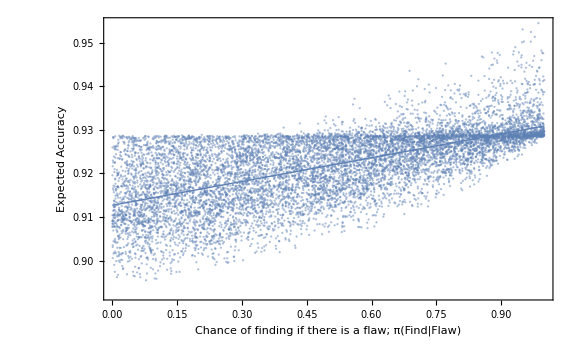

```mathematica
lm=LinearModelFit[results,x,x];
lm["RSquared"]

Show[ListPlot[results,
PlotStyle->Opacity[0.5],
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Expected Accuracy",FontSize->14],None},{Style["Chance of finding if there is a flaw; π(Find|Flaw)",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]]
,
Plot[Normal[lm],{x,0,1},
PlotStyle->Thick]]
```

Similar results happen if we use different priors in q and/or different range in the size of gBumps:

```mathematica
numTrials = 10000;
qPrior=0.7;
results=Reap[Do[
gBump = RandomReal[{0,Min[{0.1,1-qPrior}]}];
pFind = RandomReal[{0,1}];
frame=getBBCondQCSModel[qPrior,gBump,pFind];
size=Length[frame];
prior = frame[[1]];
expPrior = MatrixPower[frame,2][[1]];
inAccVec=getGlobPartitionInAcc[frame,#]&/@Range[size];
accVec = 1-inAccVec;
(*ambVec = getGlobPartitionSdAmb[frame,#]&/@Range[size];*)
Sow[{ pFind,prior.accVec}]
,numTrials]][[2,1]];
```

0.393123

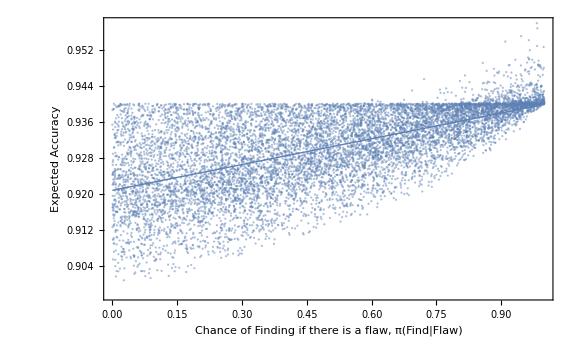

```mathematica
lm=LinearModelFit[results,x,x];
lm["RSquared"]

Show[ListPlot[results,
PlotStyle->Opacity[0.5],
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Expected Accuracy",FontSize->14],None},{Style["Chance of Finding if there is a flaw, π(Find|Flaw)",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]]
,
Plot[Normal[lm],{x,0,1},
PlotStyle->Thick]]
```

Given this, we want to simulate how often expected accuracy will lead you to prefer to scrutinize incongruent studies over congruent ones, as a function of how much more likely (on average) you are to find flaws in the former.  We fix a given prior, and then let pBump be a parameter that puts a minimum on how likely you are to find a flaw in the incongruent study, and 1–pBump gives the maximum of how likely you are to find a flaw in the congruent study.  By letting pBump vary from 0, to 0.1, ... to 1, and within each generating 500 pairs and recording the proportion which have higher expected accuracy for scrutinizing the incongruent study, we see that the degree of selective scrutiny increases with this rate:

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
Clear[rate];
Clear[results];
qPrior = 0.5;

Do[pBump = iter;

results[iter] =Reap[Do[
(*pFind2 is above on average*)
pFind1 = RandomReal[{0,1-pBump}];
pFind2 = RandomReal[{0+pBump,1}];
gBump1= RandomReal[{0,Max[{-0.2,-qPrior}]}];
gBump2= RandomReal[{0,Min[{0.2,1-qPrior}]}];
frame1 = getBBCondQCSModel[qPrior,gBump1,pFind1];
frame2 = getBBCondQCSModel[qPrior,gBump2,pFind2];

size = Length[frame1];
prior1 = frame1[[1]];
inAccVec1=getGlobPartitionInAcc[frame1,#]&/@Range[size];
accVec1 = 1-inAccVec1;
expAcc1 = prior1.accVec1;

size = Length[frame2];
prior2 = frame2[[1]];
inAccVec2=getGlobPartitionInAcc[frame2,#]&/@Range[size];
accVec2 = 1-inAccVec2;
expAcc2 = prior2.accVec2;
Sow[expAcc2 > expAcc1];
,500]][[2,1]];
results[iter] = results[iter]/.{True->1,False->0};
rate[iter]=Total[results[iter]]/Length[results[iter]]//N
,
{iter,0,1,0.1}]

rateSeq = {#,Around[Interval[MeanCI[results[#]]]]}&/@Range[0,1,0.1];

ListLinePlot[rateSeq,
PlotStyle->Dashed,
PlotMarkers->Automatic,
PlotRange->{{-0.01,1.01},{.4,1}},
ImageSize->Large,
Frame->{{True,False},{True,False}},
FrameLabel->{{Style[StringForm["Proportion favoring scrutinizing incongruent"],FontSize->14],None},{Style[StringForm["Average increase in probability of finding flaw in incongruent"],FontSize->14],None}},
FrameTicks-> {{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->Directive[FontSize->14]]
```

StudentTCI::badse: Warning: Standard error 0 is normally a positive quantity.

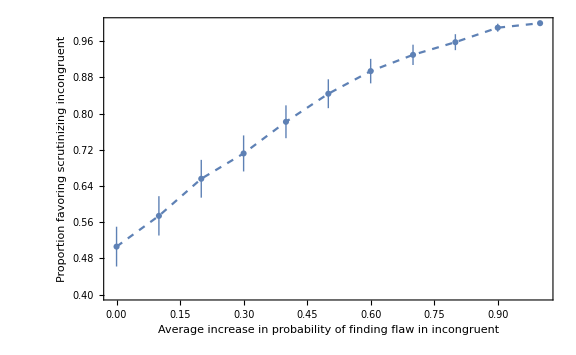

We’re now in a position to simulate what happens when two groups of agents are presented with a series of pairs of studies to scrutinize. One group (red) is on average better at finding flaws in the studies that tells against q; the other group (blue) is on average better at finding flaws in studies that tell in favor of q.  There are a variety of choice-points in the simulation; see Appendix C for some discussion.

Note certain finicky things about this simulation: 
– Strange things happen when the minpFind and maxpFind are allowed to go all the way to 0 and 1; this may be simply from non-linearities which lead to massive drops in credence when you fail to find a flaw, OR it may be an error in the code which I’ve been unable to locate
– Although increasing findGap generally increases the degree of polarization, it is not quite linear—and as it gets very large (0.8 or 0.9) the polarization starts to shrink a bit—perhaps due to the same issue that causes the above issue when minpFind and maxpFind are too extreme.
– Note that “confGBump”, “confpFind”, etc. refer to parameters of the study that is expectably confirmatory for q, meaning that if a flaw is found it RAISES the credence in q.  Thus it does NOT refer to the study that confirms q, and in which finding a flw would lead you to lower your credence in q.  Vice versa for disConfGBump, etc.

{31.537,Null}

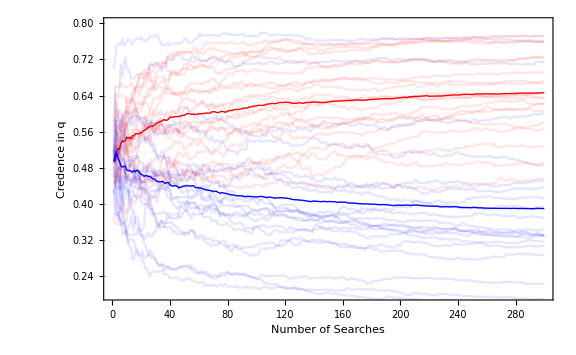

```mathematica
q={2,4,6};
numSearches = 300;
numAgents=20;
(*rate at which opinions solidify / change less at each update:*)
hardenSpeed = 0.5;
(*differential probabilities of finding errors; between 0–0.8:*)
findGap = 0.5;
minpFind = 0.1;
maxpFind = 0.9;

Timing[Do[iter;
Do[agIter;
If[iter=="pro",ag[agIter,est]=0.5];
If[iter=="con",ag[agIter,est]=0.5];
ag[agIter,weight]=10;

newTraj[agIter,iter]=Reap[Do[
(*get the pFinds for study*)
If[iter=="pro",confpFind=RandomReal[{minpFind +findGap,maxpFind}]; disConfpFind = RandomReal[{minpFind,maxpFind-findGap}];];
If[iter=="con",confpFind=RandomReal[{minpFind,maxpFind-findGap}]; disConfpFind = RandomReal[{minpFind+findGap,maxpFind}];];; 

(*Set how far might shift opinion at each stage:*)
range = Min[ag[agIter,est],1-ag[agIter,est]];
confGBump = (RandomReal[{0,range}]/(hardenSpeed*ag[agIter,weight]));
disConfGBump = (RandomReal[{-range,0}]/(hardenSpeed*ag[agIter,weight]));

frameS1 = getBBCondQCSModel[ag[agIter,est],confGBump,confpFind];
frameS2 = getBBCondQCSModel[ag[agIter,est],disConfGBump,disConfpFind];

inAccVecS1 = getGlobPartitionInAcc[frameS1,#]&/@Range[Length[frameS1]];
inAccVecS2 = getGlobPartitionInAcc[frameS2,#]&/@Range[Length[frameS2]];
expInAccS1 = frameS1[[1]].inAccVecS1;
expInAccS2=frameS2[[1]].inAccVecS2;


If[expInAccS1≤expInAccS2,
chosenFrame = frameS1;
chosenPFind = confpFind;
,
chosenFrame=frameS2;
chosenPFind=disConfpFind;
];
priorG = probability[chosenFrame[[1]],{4,5,6,7}];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
(*make posterior GG, with chance matching pFindS1*)
If[RandomVariate[BernoulliDistribution[chosenPFind]]==1,
(*Make posterior GG*)
ag[agIter,est]=probability[chosenFrame[[6]],q];
ag[agIter,weight]+=1;
,
(*if don't find, posterior is GB*)
ag[agIter,est]=probability[chosenFrame[[4]],q];
ag[agIter,weight]+=1
];
,
(*make posterior BB*)
ag[agIter,est]=probability[chosenFrame[[2]],q];;
ag[agIter,weight]+=1
];
Sow[{ag[agIter,weight]-10,ag[agIter,est]}];
,numSearches]][[2,1]];
,{agIter,numAgents}],
{iter,{"pro","con"}}]
]

proTrajs = newTraj[#,"pro"]&/@Range[numAgents];
avgProTraj = Mean[proTrajs];
conTrajs=newTraj[#,"con"]&/@Range[numAgents];
avgConTraj=Mean[conTrajs];

Show[ListLinePlot[proTrajs,
PlotStyle->Directive[Red,Opacity[0.1]],
PlotRange->{{0,numSearches},{0.2,0.8}},
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Credence in q",FontSize->14],None},{Style["Number of Searches",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]
],
ListLinePlot[avgProTraj,
PlotStyle->Directive[Red,Thick]],

ListLinePlot[conTrajs,
PlotStyle->Directive[Blue,Opacity[0.1]]],
ListLinePlot[avgConTraj,
PlotStyle->Directive[Blue,Thick]]
]
```

### Robustness checks

The following code simulates 100 “pro” (red) agents and finds their mean posterior confidence after 300 searches, along with a 95% confidence interval for that mean:

```mathematica
q={2,4,6};
numSearches = 300;
numAgents=100;
(*rate at which opinions solidify / change less at each update:*)
hardenSpeed = 0.5;
(*differential probabilities of finding errors; between 0–0.8:*)
findGap = 0.5;
minpFind = 0.1;
maxpFind = 0.9;

Timing[Do[iter;
Do[agIter;
If[iter=="pro",ag[agIter,est]=0.5];
If[iter=="con",ag[agIter,est]=0.5];
ag[agIter,weight]=10;

newTraj[agIter,iter]=Reap[Do[
(*get the pFinds for study*)
If[iter=="pro",confpFind=RandomReal[{minpFind +findGap,maxpFind}]; disConfpFind = RandomReal[{minpFind,maxpFind-findGap}];];
If[iter=="con",confpFind=RandomReal[{minpFind,maxpFind-findGap}]; disConfpFind = RandomReal[{minpFind+findGap,maxpFind}];];; 

(*Set how far might shift opinion at each stage:*)
range = Min[ag[agIter,est],1-ag[agIter,est]];
confGBump = (RandomReal[{0,range}]/(hardenSpeed*ag[agIter,weight]));
disConfGBump = (RandomReal[{-range,0}]/(hardenSpeed*ag[agIter,weight]));

frameS1 = getBBCondQCSModel[ag[agIter,est],confGBump,confpFind];
frameS2 = getBBCondQCSModel[ag[agIter,est],disConfGBump,disConfpFind];

inAccVecS1 = getGlobPartitionInAcc[frameS1,#]&/@Range[Length[frameS1]];
inAccVecS2 = getGlobPartitionInAcc[frameS2,#]&/@Range[Length[frameS2]];
expInAccS1 = frameS1[[1]].inAccVecS1;
expInAccS2=frameS2[[1]].inAccVecS2;


If[expInAccS1≤expInAccS2,
chosenFrame = frameS1;
chosenPFind = confpFind;
,
chosenFrame=frameS2;
chosenPFind=disConfpFind;
];
priorG = probability[chosenFrame[[1]],{4,5,6,7}];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
(*make posterior GG, with chance matching pFindS1*)
If[RandomVariate[BernoulliDistribution[chosenPFind]]==1,
(*Make posterior GG*)
ag[agIter,est]=probability[chosenFrame[[6]],q];
ag[agIter,weight]+=1;
,
(*if don't find, posterior is GB*)
ag[agIter,est]=probability[chosenFrame[[4]],q];
ag[agIter,weight]+=1
];
,
(*make posterior BB*)
ag[agIter,est]=probability[chosenFrame[[2]],q];;
ag[agIter,weight]+=1
];
Sow[{ag[agIter,weight]-10,ag[agIter,est]}];
,numSearches]][[2,1]];
,{agIter,numAgents}],
{iter,{"pro"}}]
];
posteriors = ag[#,est]&/@Range[numAgents];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

0.600018

{0.575308,0.624729}

The following code does the same for 100 “con” (blue) agents:

```mathematica
q={2,4,6};
numSearches = 300;
numAgents=100;
(*rate at which opinions solidify / change less at each update:*)
hardenSpeed = 0.5;
(*differential probabilities of finding errors; between 0–0.8:*)
findGap = 0.5;
minpFind = 0.1;
maxpFind = 0.9;

Timing[Do[iter;
Do[agIter;
If[iter=="pro",ag[agIter,est]=0.5];
If[iter=="con",ag[agIter,est]=0.5];
ag[agIter,weight]=10;

newTraj[agIter,iter]=Reap[Do[
(*get the pFinds for study*)
If[iter=="pro",confpFind=RandomReal[{minpFind +findGap,maxpFind}]; disConfpFind = RandomReal[{minpFind,maxpFind-findGap}];];
If[iter=="con",confpFind=RandomReal[{minpFind,maxpFind-findGap}]; disConfpFind = RandomReal[{minpFind+findGap,maxpFind}];];; 

(*Set how far might shift opinion at each stage:*)
range = Min[ag[agIter,est],1-ag[agIter,est]];
confGBump = (RandomReal[{0,range}]/(hardenSpeed*ag[agIter,weight]));
disConfGBump = (RandomReal[{-range,0}]/(hardenSpeed*ag[agIter,weight]));

frameS1 = getBBCondQCSModel[ag[agIter,est],confGBump,confpFind];
frameS2 = getBBCondQCSModel[ag[agIter,est],disConfGBump,disConfpFind];

inAccVecS1 = getGlobPartitionInAcc[frameS1,#]&/@Range[Length[frameS1]];
inAccVecS2 = getGlobPartitionInAcc[frameS2,#]&/@Range[Length[frameS2]];
expInAccS1 = frameS1[[1]].inAccVecS1;
expInAccS2=frameS2[[1]].inAccVecS2;


If[expInAccS1≤expInAccS2,
chosenFrame = frameS1;
chosenPFind = confpFind;
,
chosenFrame=frameS2;
chosenPFind=disConfpFind;
];
priorG = probability[chosenFrame[[1]],{4,5,6,7}];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
(*make posterior GG, with chance matching pFindS1*)
If[RandomVariate[BernoulliDistribution[chosenPFind]]==1,
(*Make posterior GG*)
ag[agIter,est]=probability[chosenFrame[[6]],q];
ag[agIter,weight]+=1;
,
(*if don't find, posterior is GB*)
ag[agIter,est]=probability[chosenFrame[[4]],q];
ag[agIter,weight]+=1
];
,
(*make posterior BB*)
ag[agIter,est]=probability[chosenFrame[[2]],q];;
ag[agIter,weight]+=1
];
Sow[{ag[agIter,weight]-10,ag[agIter,est]}];
,numSearches]][[2,1]];
,{agIter,numAgents}],
{iter,{"con"}}]
];
posteriors = ag[#,est]&/@Range[numAgents];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

0.390331

{0.370068,0.410594}

When I ran the above code, I received mean posteriors for the “pro” group at 0.600 with a 95% confidence interval of [0.575, 0.624] and mean posteriors for the “con” group at 0.390 with a 95% confidence interval of [0.370, 0.411].

We can also check robustness by varying the parameters of the simulation.The following code displays the results from varying findGap from 0, 0.2, 0.5, 0.7, as well as hardenSpeed from 0.3 and 0.6, all for 200 searched and 20 agents.

findGap = 0, hardenSpeed = 0.3, numAgents = 20, numSearches = 200, simulation time = 22.5376

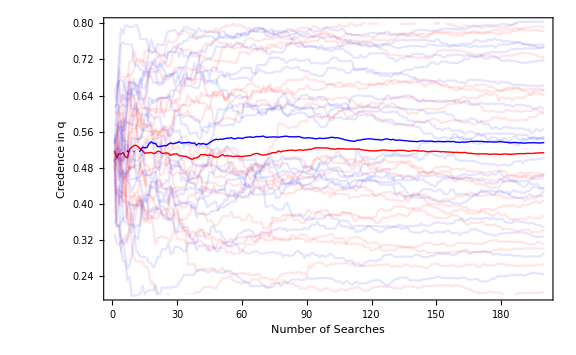

findGap = 0, hardenSpeed = 0.6, numAgents = 20, numSearches = 200, simulation time = 23.1892

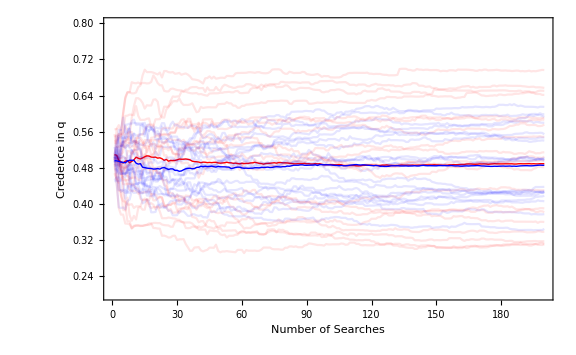

findGap = 0.2, hardenSpeed = 0.3, numAgents = 20, numSearches = 200, simulation time = 23.1323

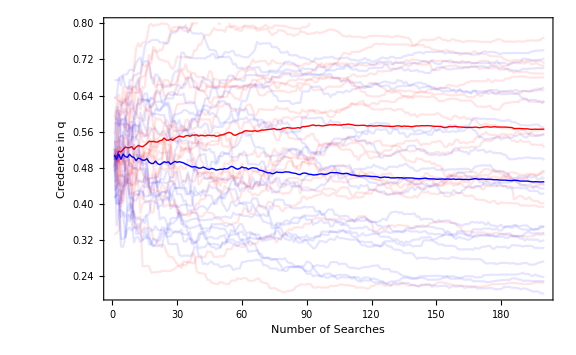

findGap = 0.2, hardenSpeed = 0.6, numAgents = 20, numSearches = 200, simulation time = 23.1017

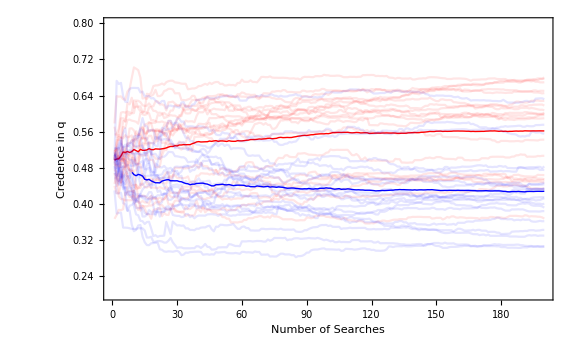

findGap = 0.6, hardenSpeed = 0.3, numAgents = 20, numSearches = 200, simulation time = 22.9706

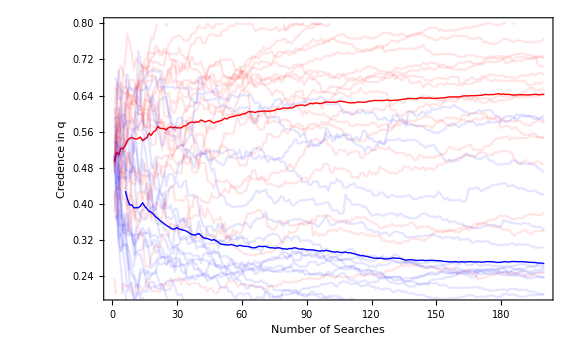

findGap = 0.6, hardenSpeed = 0.6, numAgents = 20, numSearches = 200, simulation time = 22.9977

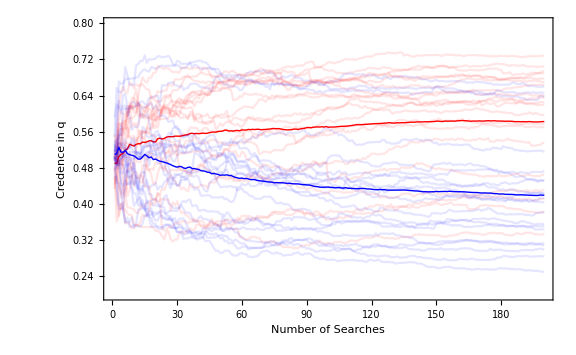

findGap = 0.8, hardenSpeed = 0.3, numAgents = 20, numSearches = 200, simulation time = 26.1226

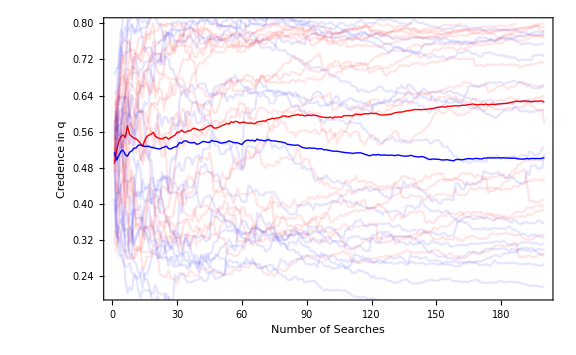

findGap = 0.8, hardenSpeed = 0.6, numAgents = 20, numSearches = 200, simulation time = 24.7324

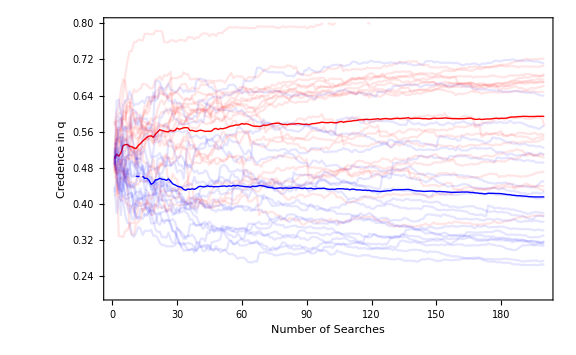

```mathematica
q={2,4,6};
numSearches = 200;
numAgents=20;
minpFind = 0.1;
maxpFind = 0.9;

Do[findGap = findGapIter;
Do[hardenSpeed = hardenIter;
simTime = Timing[Do[iter;
Do[agIter;
If[iter=="pro",ag[agIter,est]=0.5];
If[iter=="con",ag[agIter,est]=0.5];
ag[agIter,weight]=10;

newTraj[agIter,iter]=Reap[Do[
(*get the pFinds for study*)
If[iter=="pro",confpFind=RandomReal[{minpFind +findGap,maxpFind}]; disConfpFind = RandomReal[{minpFind,maxpFind-findGap}];];
If[iter=="con",confpFind=RandomReal[{minpFind,maxpFind-findGap}]; disConfpFind = RandomReal[{minpFind+findGap,maxpFind}];];; 

(*Set how far might shift opinion at each stage:*)
range = Min[ag[agIter,est],1-ag[agIter,est]];
confGBump = (RandomReal[{0,range}]/(hardenSpeed*ag[agIter,weight]));
disConfGBump = (RandomReal[{-range,0}]/(hardenSpeed*ag[agIter,weight]));

frameS1 = getBBCondQCSModel[ag[agIter,est],confGBump,confpFind];
frameS2 = getBBCondQCSModel[ag[agIter,est],disConfGBump,disConfpFind];

inAccVecS1 = getGlobPartitionInAcc[frameS1,#]&/@Range[Length[frameS1]];
inAccVecS2 = getGlobPartitionInAcc[frameS2,#]&/@Range[Length[frameS2]];
expInAccS1 = frameS1[[1]].inAccVecS1;
expInAccS2=frameS2[[1]].inAccVecS2;


If[expInAccS1≤expInAccS2,
chosenFrame = frameS1;
chosenPFind = confpFind;
,
chosenFrame=frameS2;
chosenPFind=disConfpFind;
];
priorG = probability[chosenFrame[[1]],{4,5,6,7}];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
(*make posterior GG, with chance matching pFindS1*)
If[RandomVariate[BernoulliDistribution[chosenPFind]]==1,
(*Make posterior GG*)
ag[agIter,est]=probability[chosenFrame[[6]],q];
ag[agIter,weight]+=1;
,
(*if don't find, posterior is GB*)
ag[agIter,est]=probability[chosenFrame[[4]],q];
ag[agIter,weight]+=1
];
,
(*make posterior BB*)
ag[agIter,est]=probability[chosenFrame[[2]],q];;
ag[agIter,weight]+=1
];
Sow[{ag[agIter,weight]-10,ag[agIter,est]}];
,numSearches]][[2,1]];
,{agIter,numAgents}],
{iter,{"pro","con"}}]
][[1]];

proTrajs = newTraj[#,"pro"]&/@Range[numAgents];
avgProTraj = Mean[proTrajs];
conTrajs=newTraj[#,"con"]&/@Range[numAgents];
avgConTraj=Mean[conTrajs];

Print[StringForm["findGap = ``, hardenSpeed = ``, numAgents = ``, numSearches = ``, simulation time = ``", findGap,hardenSpeed,numAgents, numSearches,simTime]];
Print[Show[ListLinePlot[proTrajs,
PlotStyle->Directive[Red,Opacity[0.1]],
PlotRange->{{0,numSearches},{0.2,0.8}},
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Credence in q",FontSize->14],None},{Style["Number of Searches",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]
],
ListLinePlot[avgProTraj,
PlotStyle->Directive[Red,Thick]],

ListLinePlot[conTrajs,
PlotStyle->Directive[Blue,Opacity[0.1]]],
ListLinePlot[avgConTraj,
PlotStyle->Directive[Blue,Thick]]
]];
,{hardenIter,{0.3,0.6}}];
,{findGapIter,{0,0.2,0.5,0.7}}];
```

## 2) Argument models

The getArgModel function generates an argument model with a given set of parameters.  It takes the prior probability of q (priorQ), the probability of q if the argument is good (gInf), the confidence you should have THAT the argument is good if indeed it is (gConf), the probability of q if the argument is bad (bInf), and the confidence you should have THAT the argument is bad if indeed it is (bConf).

NOTES: 
–  {2,4} represents the proposition q.
– Given the constraints, the function solves for the prior probability of G, π(G).  In order to satisfy the value of evidence, we must have gConf ≥ π(G) and bConf ≥ π(G) = 1 – π(G).  If the parameters you input violate this constraint, the function will output an Error.
– Make sure the input parameters are all between 0 and 1
– This function WILL allow you to make the argument more ambiguous if it’s bad (B = {4,5}) than if it’s good (G = {2,3}); but that would violate its intended interpretation.

```mathematica
getArgModel[priorQ_,gInf_,gConf_,bInf_,bConf_]:=
(*{2,4} is the claim q *)
((*get prior confidence that in good case:*)
priorG =x/.Solve[priorQ==x*(gInf)+(1-x)(bInf),x][[1]];
If[priorG>gConf,Print["gConf below priorG"]];
If[1-priorG > bConf, Print["bConf below 1-priorG"]];

(*Generate frame:*)
Return[{{0,priorG*gInf,priorG*(1-gInf),(1-priorG)(bInf),(1-priorG)(1-bInf)},
{0,gConf*gInf,gConf(1-gInf), (1-gConf)bInf,(1-gConf)(1-bInf)},
{0,gConf*gInf,gConf(1-gInf), (1-gConf)bInf,(1-gConf)(1-bInf)},
{0,(1-bConf)*gInf,(1-bConf)(1-gInf),bConf*bInf,bConf(1-bInf)},
{0,(1-bConf)*gInf,(1-bConf)(1-gInf),bConf*bInf,bConf(1-bInf)}}]
)
```

For example, here’s an argument model in which you start out 50-50 in q (and 50-50 the argument will be good); conditional on the argument being good your credence is 0.8; conditional on it being bad it’s 0.2; but if it’s good you should be 0.9 confident of this, while if it’s bad you should only be 0.6 confident of this:

```mathematica
frame = getArgModel[0.5,0.8,0.9,0.2,0.6]
MatrixForm[frame]
```

{{0,0.4,0.1,0.1,0.4},{0,0.72,0.18,0.02,0.08},{0,0.72,0.18,0.02,0.08},{0,0.32,0.08,0.12,0.48},{0,0.32,0.08,0.12,0.48}}

(0 | 0.4 | 0.1 | 0.1 | 0.4
0 | 0.72 | 0.18 | 0.02 | 0.08
0 | 0.72 | 0.18 | 0.02 | 0.08
0 | 0.32 | 0.08 | 0.12 | 0.48
0 | 0.32 | 0.08 | 0.12 | 0.48)

Thus the posterior probability in q ( = {2,4}) is either 0.74 or 0.44:

```mathematica
probability[frame[[2]],{2,4}]
probability[frame[[3]],{2,4}]
probability[frame[[4]],{2,4}]
probability[frame[[5]],{2,4}]
```

0.74

0.74

0.44

0.44

Each is initially 50-50 likely:

```mathematica
probability[frame[[1]],{2,3}]
probability[frame[[1]],{4,5}]
```

0.5

0.5

The prior credence in q is 0.5:

```mathematica
probability[frame[[1]],{2,4}]
```

0.5

And yet the expected future rational credence is  0.59 > 0.5. We can take the prior’s expectation of P, E_π(P) by multiplying it by the frame:

```mathematica
expP = frame[[1]].frame
```

{0.,0.52,0.13,0.07,0.28}

And then note that this expectation of P assigns 0.59 to q:

```mathematica
probability[expP,{2,4}]
```

0.59

We now want to be able to generate random argument models that either favor q (so π(q | G) > π(q), and the argument is less ambiguous if G than if B), or which disfavor q (so π(q | G) < π(q), and the argument is less ambiguous if G than if B).

getRandFavShiftArgModel generates an argument-model that favors q.  It takes a prior probability of q, priorQ, a constraint on how far this probability of q is allowed to shift, shiftCons, and a prior probability that the argument is good, priorG, and generates a random favorable argument within those parameter constraints

```mathematica
getRandFavShiftArgModel[priorQ_,shiftCons_,priorG_]:=(cons=Quiet[Reduce[priorQ==priorG g+(1-priorG) b&&0≤g≤1&&Abs[priorQ-g]≤shiftCons&&0≤b≤1&&Abs[priorQ-b]≤shiftCons]];gMax=Maximize[{g,cons},{g,b}]⟦1⟧;gInf=RandomReal[{priorQ,Min[1,priorQ+shiftCons,gMax]}];bInf=b/.Solve[priorQ==priorG gInf+(1-priorG) b,b]⟦1⟧;
gShift = RandomReal[{0,1-priorG}];
(*make sure doesn't exceed 1, and doesn't exceeed gShift*)
bShift = RandomReal[{0,Min[gShift,priorG]}];
bConf=(1-priorG)+bShift;
gConf=priorG+gShift;
Return[getArgModel[priorQ,gInf,gConf,bInf,bConf]])
```

For example:

```mathematica
frame = getRandFavShiftArgModel[0.5,0.2,0.5];
MatrixForm[frame]
```

(0 | 0.339226 | 0.160774 | 0.160774 | 0.339226
0 | 0.491831 | 0.233101 | 0.0884476 | 0.18662
0 | 0.491831 | 0.233101 | 0.0884476 | 0.18662
0 | 0.286132 | 0.135611 | 0.185938 | 0.39232
0 | 0.286132 | 0.135611 | 0.185938 | 0.39232)

```mathematica
probability[frame[[2]],{2,4}]
```

0.580279

getRandDisShiftArgModel does exactly the same thing, except it makes π(q | G) < π(q)

```mathematica
a[priorQ_,shiftCons_,priorG_]:=(cons=Quiet[Reduce[priorQ==priorG g+(1-priorG) b&&0≤g≤1&&Abs[priorQ-g]≤shiftCons&&0≤b≤1&&Abs[priorQ-b]≤shiftCons]];gMin=Minimize[{g,cons},{g,b}]⟦1⟧;gInf=RandomReal[{priorQ,Max[0,priorQ-shiftCons,gMin]}];bInf=b/.Solve[priorQ==priorG gInf+(1-priorG) b,b]⟦1⟧;
gShift = RandomReal[{0,1-priorG}];
(*make sure doesn't exceed 1, and doesn't exceeed gShift*)
(*Note: this makes them DEPENDENT, so whatever gShift happens to be, bShift is lower. Might want to make independent, but with bShift having a tighter bound*)
bShift = RandomReal[{0,Min[gShift,priorG]}];
bConf=(1-priorG)+bShift;
gConf=priorG+gShift;
Return[getArgModel[priorQ,gInf,gConf,bInf,bConf]])
```

```mathematica
frame = getRandDisShiftArgModel[0.5,0.2,0.5];
MatrixForm[frame]
```

(0 | 0.197646 | 0.302354 | 0.302354 | 0.197646
0 | 0.274225 | 0.419502 | 0.185206 | 0.121067
0 | 0.274225 | 0.419502 | 0.185206 | 0.121067
0 | 0.158231 | 0.242059 | 0.362649 | 0.237061
0 | 0.158231 | 0.242059 | 0.362649 | 0.237061)

```mathematica
probability[frame[[2]],{2,4}]
```

0.45943

Given these two functions, we can simulate presenting a group of (red) agents with random arguments that favor q, and a separate group of (blue) agents with random arguments that disfavor q.

numAgents = the number of agents in each group
numArgs = the number of arguments each agent sees
baseShift = the base constraint on how far arguments could in principle move opinions; range between 0–0.5.  (Depending on hardenSpeed, the amount of shift may be less extreme than its raw number)
hardenSpeed = how quickly the shift induced by each argument tapers off.  Recommended between 0.2–0.5

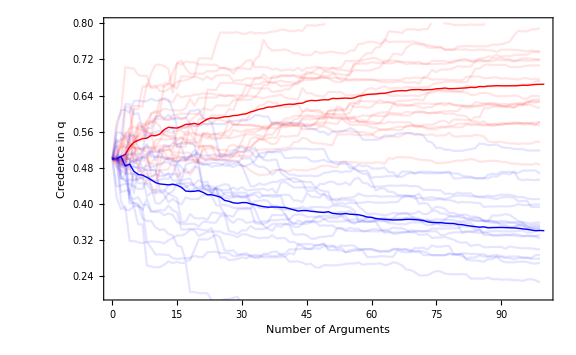

Simulation time = 50.6017

```mathematica
Clear[ag];
Clear[traj];
numAgents=20;
numArgs=100;

baseShift = 0.4;

hardenSpeed = 0.2;
(*hardening = True;
If[hardening==True,harden[x_]:=Sqrt[x]]
If[hardening==False, harden[x_]:=1]*)

simTime = Timing[Do[
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandDisShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"pro","con"}}]][[1]];
Beep[]

Clear[allAgents];
allAgents["pro"] = ag[traj,#,"pro"]&/@Range[numAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["pro"]=Table[{iter1,Mean[ag[traj,#,"pro"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];
avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Show[ListLinePlot[allAgents["pro"],
PlotStyle->Directive[Red,Opacity[0.1]],
PlotRange->{{0,numArgs},{0.2,0.8}},
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Credence in q",FontSize->14],None},{Style["Number of Arguments",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]
],
ListLinePlot[avgAgents["pro"],
PlotStyle->Directive[Red,Thick]],

ListLinePlot[allAgents["con"],
PlotStyle->Directive[Blue,Opacity[0.1]]],
ListLinePlot[avgAgents["con"],
PlotStyle->Directive[Blue,Thick]]
]
Print[StringForm["Simulation time = ``",simTime]]
```

The following simulation lets you vary what proportion of the arguments are good.  Whereas the above pulled π(G) randomly between [0,1] for both sides, this one pulls π(G) from [favGBound,1] for the “pro” side, and π(G) from [0, 1–favGBound] for the “con” side.  

The following code runs the simulation for 30 agents and 50 arguments with favGBound at 0, 0.25, 0.5, 0.75, and 0.95:

Simulation time = 44.7012, favGBound = 0

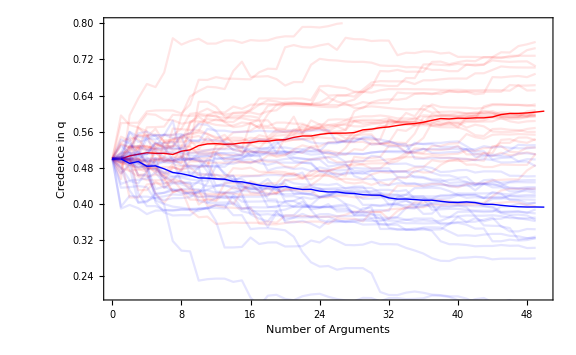

Simulation time = 42.0477, favGBound = 0.25

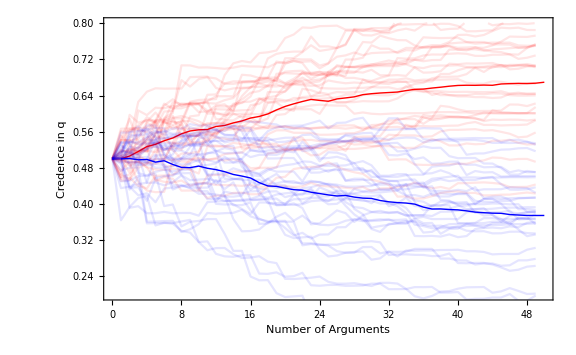

Simulation time = 38.1415, favGBound = 0.5

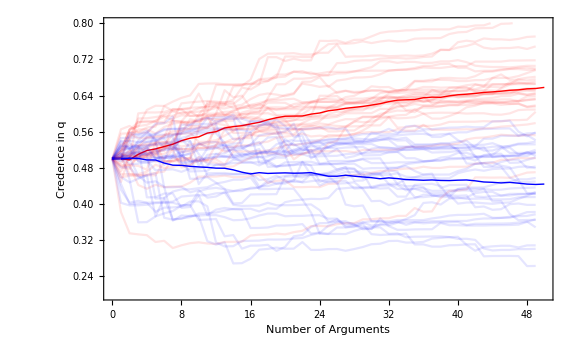

Simulation time = 40.718, favGBound = 0.75

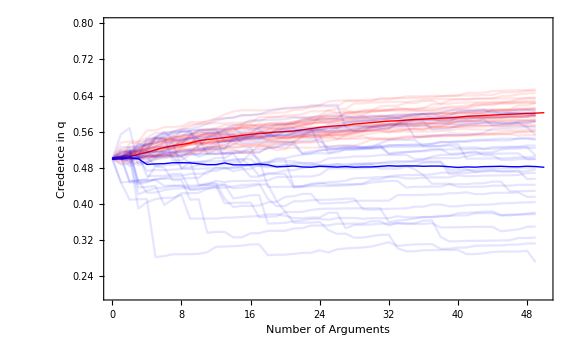

Simulation time = 42.6826, favGBound = 0.95

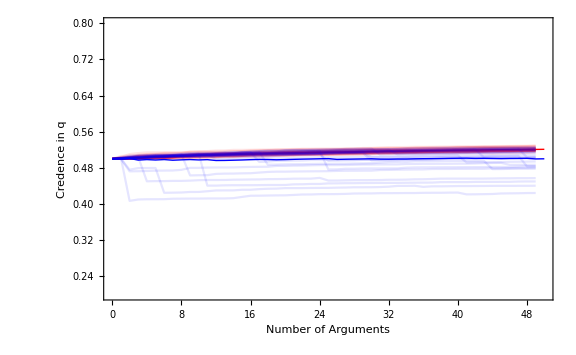

```mathematica
numAgents=30;
numArgs=50;

Do[favGBound = boundIter;

Clear[ag];
Clear[traj];
baseShift = 0.4;
hardenSpeed = 0.2;
(*hardening = True;
If[hardening==True,harden[x_]:=Sqrt[x]]
If[hardening==False, harden[x_]:=1]*)

simTime = Timing[Do[
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{favGBound,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1-favGBound}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandDisShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"pro","con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["pro"] = ag[traj,#,"pro"]&/@Range[numAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["pro"]=Table[{iter1,Mean[ag[traj,#,"pro"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];
avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["Simulation time = ``, favGBound = ``",simTime,favGBound]];
Print[Show[ListLinePlot[allAgents["pro"],
PlotStyle->Directive[Red,Opacity[0.1]],
PlotRange->{{0,numArgs},{0.2,0.8}},
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Credence in q",FontSize->14],None},{Style["Number of Arguments",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]
],
ListLinePlot[avgAgents["pro"],
PlotStyle->Directive[Red,Thick]],

ListLinePlot[allAgents["con"],
PlotStyle->Directive[Blue,Opacity[0.1]]],
ListLinePlot[avgAgents["con"],
PlotStyle->Directive[Blue,Thick]]
]];
,{boundIter,{0,0.25,0.5,0.75,0.95}}]
```

### Robustness

Again there are two main ways to check for robustness. 

First, we can run the same simulation with 100 favorable-argument (red) agents to get  95% confidence intervals for their mean posteriors:

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
Clear[ag];
Clear[traj];
numAgents=100;
numArgs=100;

baseShift = 0.4;

hardenSpeed = 0.2;
(*hardening = True;
If[hardening==True,harden[x_]:=Sqrt[x]]
If[hardening==False, harden[x_]:=1]*)

simTime = Timing[Do[
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandDisShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"pro"}}]][[1]];
posteriors = ag[cred,#,"pro"]&/@Range[numAgents];
Print[StringForm["Simulation time = ``",simTime]];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

Simulation time = 128.634

0.662972

{0.641563,0.684381}

```mathematica
Beep[]
```

The following does the same for 100 disfavorable-argument (blue) agents:

```mathematica
Clear[ag];
Clear[traj];
numAgents=100;
numArgs=100;

baseShift = 0.4;

hardenSpeed = 0.2;
(*hardening = True;
If[hardening==True,harden[x_]:=Sqrt[x]]
If[hardening==False, harden[x_]:=1]*)

simTime = Timing[Do[
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandDisShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"con"}}]][[1]];
posteriors = ag[cred,#,"con"]&/@Range[numAgents];
Print[StringForm["Simulation time = ``",simTime]];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

Simulation time = 133.785

0.341809

{0.320695,0.362923}

When I ran the above code, I received mean posteriors for the favorable-argument group at 0.663 with a 95% confidence interval of [0.642, 0.684] and mean posteriors for the disfavorable-argument group at 0.342 with a 95% confidence interval of [0.321, 0.363].

The next way to check robustness is to vary our parameters systematically. numAgents and numArgs are straightforward; the following code varies baseShift from {0.2, 0.4}, and hardenSpeed from {0.1,0.3,0.5}

baseShift = 0.2, hardenSpeed = 0.1, Simulation time = 33.3015

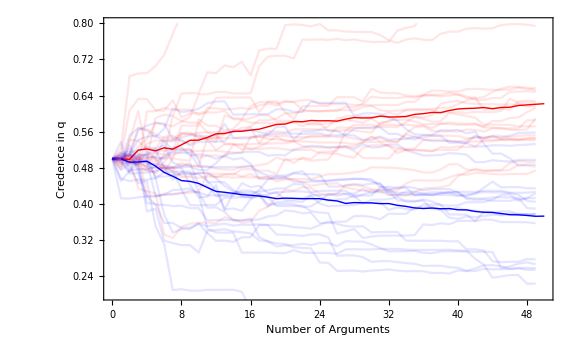

baseShift = 0.2, hardenSpeed = 0.3, Simulation time = 31.9777

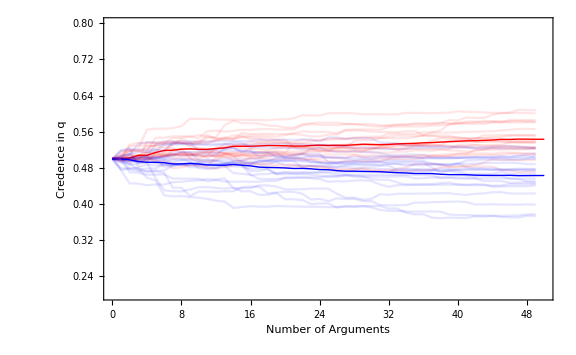

baseShift = 0.2, hardenSpeed = 0.5, Simulation time = 27.83

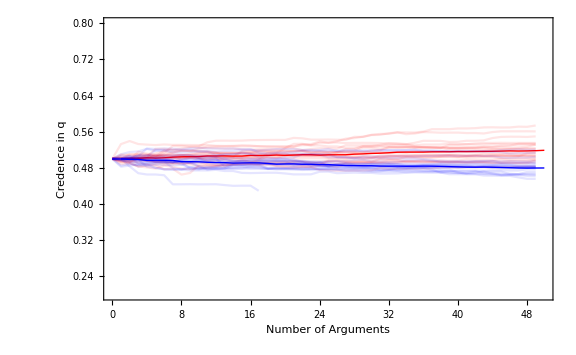

baseShift = 0.4, hardenSpeed = 0.1, Simulation time = 26.4426

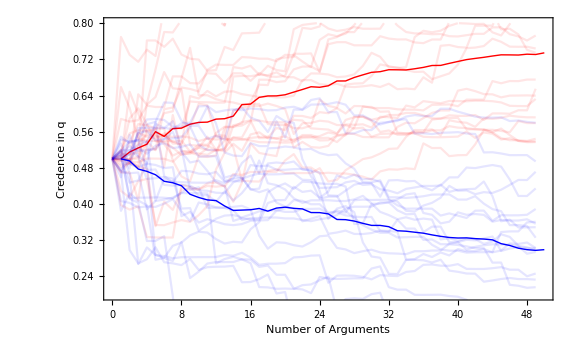

baseShift = 0.4, hardenSpeed = 0.3, Simulation time = 26.8643

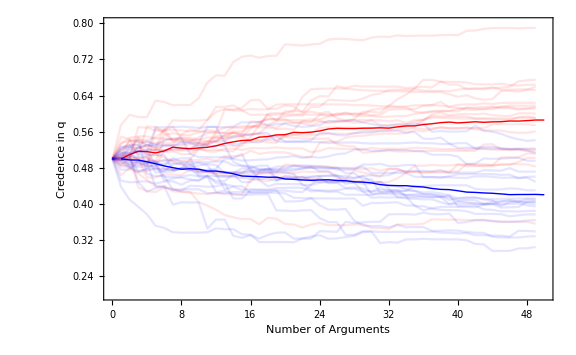

baseShift = 0.4, hardenSpeed = 0.5, Simulation time = 27.4426

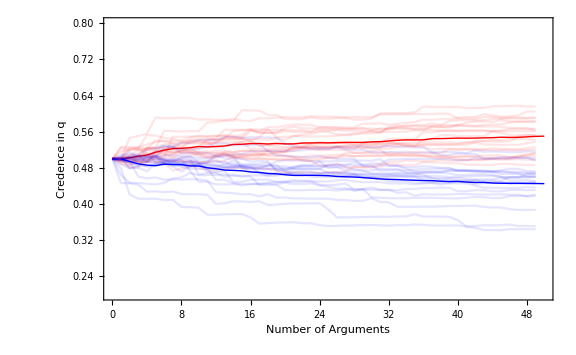

```mathematica
Clear[ag];
Clear[traj];
numAgents=20;
numArgs=50;

baseShift = 0.4;

hardenSpeed = 0.2;

Do[baseShift = baseIter;
Do[hardenSpeed = hardenIter;

simTime = Timing[Do[
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandDisShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"pro","con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["pro"] = ag[traj,#,"pro"]&/@Range[numAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["pro"]=Table[{iter1,Mean[ag[traj,#,"pro"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];
avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["baseShift = ``, hardenSpeed = ``, Simulation time = ``",baseShift, hardenSpeed,simTime]];
Print[Show[ListLinePlot[allAgents["pro"],
PlotStyle->Directive[Red,Opacity[0.1]],
PlotRange->{{0,numArgs},{0.2,0.8}},
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Credence in q",FontSize->14],None},{Style["Number of Arguments",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]
],
ListLinePlot[avgAgents["pro"],
PlotStyle->Directive[Red,Thick]],

ListLinePlot[allAgents["con"],
PlotStyle->Directive[Blue,Opacity[0.1]]],
ListLinePlot[avgAgents["con"],
PlotStyle->Directive[Blue,Thick]]
]]
,{hardenIter,{0.1,0.3,0.5}}]
,{baseIter,{0.2,0.4}}]
```

## (3) Combined Model

The extractArgPars takes an argument model and extracts the parameters needed to generate it, and loads them into the variable-names as specified in the commented section:

```mathematica
(*requires a (5-world) arg model*)
extractArgPars[frame_]:=(
(*loads up:
priorQ = prior in q before argument
gInf=informed credence in q when argument good
bInf=informed credence in q when argument bad
priorG=prior credence that argument good
priorB=prior creence that argument bad
bConf=posterior confidence that argument bad (if it is)
gConf=posterior confidence that argument good (if it is)
*)
priorQ = probability[frame[[1]],{2,4}];
gInf = frame[[2,2]]/(frame[[2,2]]+frame[[2,3]]);
bInf = frame[[4,4]]/(frame[[4,4]]+frame[[4,5]]);
(*priorG = x/.Solve[priorQ==x*(gInf)+(1-x)(bInf),x][[1]];*)
priorG = probability[frame[[1]],{2,3}];
priorB = 1-priorG;
bConf =(1-x)/.Solve[probability[frame[[4]],{2,4}]==x*gInf+(1-x)(bInf),x][[1]];gConf =x/.Solve[probability[frame[[2]],{2,4}]==x*gInf+(1-x)(bInf),x][[1]];
)
```

For example, if we get a random argument, we can extract it’s parameters and remake it:

```mathematica
frame = getRandFavShiftArgModel[0.5,0.2,0.5]
```

{{0,0.261666,0.238334,0.238334,0.261666},{0,0.460661,0.419585,0.0570828,0.0626711},{0,0.460661,0.419585,0.0570828,0.0626711},{0,0.256276,0.233424,0.243243,0.267056},{0,0.256276,0.233424,0.243243,0.267056}}

```mathematica
extractArgPars[frame]
```

```mathematica
getArgModel[priorQ,gInf,gConf,bInf,bConf]
```

{{0,0.261666,0.238334,0.238334,0.261666},{0,0.460661,0.419585,0.0570828,0.0626711},{0,0.460661,0.419585,0.0570828,0.0626711},{0,0.256276,0.233424,0.243243,0.267056},{0,0.256276,0.233424,0.243243,0.267056}}

The scrutArg function takes an argument model (frame), a probability of finding a flaw if there is one (pFind), and a degree to which scrutiny increases ambiguity (jShift), and outputs a cognitive search model that results from scrutinizing it, meeting the relevant parameters as specified in Appendix C.3:

```mathematica
(*generate scrutiny model based on argument model such that if argument is good, condition on not-finding a problem (word); and if argument bad but don't find, J-shift up on that fact*)
(*J-shift a parameter between 0 and 1 saying how much posterior conf in NfW (possibility where there's a completion you don't find) moves toward 1 from the baseline of simply conditioning on Nf*)
scrutArg[frame_,pFind_,jShift_]:=
(extractArgPars[frame];
(*loads up:
priorQ = prior in q before argument
gInf=informed credence in q when argument good
bInf=informed credence in q when argument bad
priorG=prior credence that argument good
priorB=prior creence that argument bad
bConf=posterior confidence that argument bad (if it is)
gConf=posterior confidence that argument good (if it is)
*)
(*informed probability if word is bInf, so bump is:*)
wBump = bInf - priorQ;
priorFW = priorB*pFind;
priorNfW = priorB*(1-pFind);
priorNfNw = priorG;
(*posterior confidence that no word obtained by conditioning on no find*)
postNwConf = gConf/(gConf + (1-gConf)(1-pFind));
(*posterior conf in NfW if just conditioned on Nf:*)
NfWCond = (bConf(1-pFind))/(bConf(1-pFind) + (1-bConf));
(*How much should your confidence that there's a word shift toward there being one if there is one that you don't find?*)
postNfWConf = (1-jShift)*NfWCond + jShift*1;

Return[csQModel[priorQ,wBump,priorFW,priorNfW,priorNfNw,postNfWConf,postNwConf]]
)
```

For example, here’s our above randomly-generated argument model, along with what happens when we scrutinize it:

```mathematica
MatrixForm[frame]
MatrixForm[scrutArg[frame,0.5,0.5]]
```

(0 | 0.261666 | 0.238334 | 0.238334 | 0.261666
0 | 0.460661 | 0.419585 | 0.0570828 | 0.0626711
0 | 0.460661 | 0.419585 | 0.0570828 | 0.0626711
0 | 0.256276 | 0.233424 | 0.243243 | 0.267056
0 | 0.256276 | 0.233424 | 0.243243 | 0.267056)

(0 | 0.261666 | 0.238334 | 0.119167 | 0.130833 | 0.119167 | 0.130833
0 | 0.490001 | 0.446308 | 0.0303592 | 0.0333313 | 0 | 0
0 | 0.490001 | 0.446308 | 0.0303592 | 0.0333313 | 0 | 0
0 | 0.172032 | 0.156692 | 0.319976 | 0.3513 | 0 | 0
0 | 0.172032 | 0.156692 | 0.319976 | 0.3513 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.476668 | 0.523332
0 | 0 | 0 | 0 | 0 | 0.476668 | 0.523332)

Notice a few things about this model of scrutinizing arguments.

First, when you are guaranteed to find a flaw if there is one (π(Find | Flaw) = pFind = 1), then regardless of the jShift parameter, scrutiny turns the ambiguous-evidence argument into an unambiguous update (although the possibilities in C, i.e. 4 and 5, differ from those in N, i.e. 2 and 3, the prior and N assign probability 0 to these possibilities):

```mathematica
MatrixForm[frame = getRandFavShiftArgModel[0.5,0.2,0.5]]
MatrixForm[scrutArg[frame,1,0.5]]
```

(0 | 0.325654 | 0.174346 | 0.174346 | 0.325654
0 | 0.432748 | 0.23168 | 0.117011 | 0.218561
0 | 0.432748 | 0.23168 | 0.117011 | 0.218561
0 | 0.228577 | 0.122373 | 0.226318 | 0.422732
0 | 0.228577 | 0.122373 | 0.226318 | 0.422732)

(0 | 0.325654 | 0.174346 | 0. | 0. | 0.174346 | 0.325654
0 | 0.651309 | 0.348691 | 0. | 0. | 0 | 0
0 | 0.651309 | 0.348691 | 0. | 0. | 0 | 0
0 | 0.325654 | 0.174346 | 0.174346 | 0.325654 | 0 | 0
0 | 0.325654 | 0.174346 | 0.174346 | 0.325654 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.348691 | 0.651309
0 | 0 | 0 | 0 | 0 | 0.348691 | 0.651309)

Second, if you are guaranteed not to find a flaw in the argument if there is one (you know it’s to complex), then---at least with the further plausible assumption that scrutiny adds no ambiguity (you don’t think “maybe I should’ve found it)---then scrutiny leaves the initial argument model unchanged (there is no possibility of ending up in F = {6,7}):

```mathematica
MatrixForm[frame = getRandFavShiftArgModel[0.5,0.2,0.5]]
MatrixForm[scrutArg[frame,0,0]]
```

(0 | 0.27327 | 0.22673 | 0.22673 | 0.27327
0 | 0.321346 | 0.266617 | 0.186842 | 0.225195
0 | 0.321346 | 0.266617 | 0.186842 | 0.225195
0 | 0.243994 | 0.202439 | 0.25102 | 0.302547
0 | 0.243994 | 0.202439 | 0.25102 | 0.302547)

(0 | 0.27327 | 0.22673 | 0.22673 | 0.27327 | 0. | 0.
0 | 0.321346 | 0.266617 | 0.186842 | 0.225195 | 0 | 0
0 | 0.321346 | 0.266617 | 0.186842 | 0.225195 | 0 | 0
0 | 0.243994 | 0.202439 | 0.25102 | 0.302547 | 0 | 0
0 | 0.243994 | 0.202439 | 0.25102 | 0.302547 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.453459 | 0.546541
0 | 0 | 0 | 0 | 0 | 0.453459 | 0.546541)

Finally, for values between these extremes, scrutiny makes some difference:

```mathematica
MatrixForm[frame = getRandFavShiftArgModel[0.5,0.2,0.5]]
MatrixForm[scrutArg[frame,0.5,0.5]]
```

(0 | 0.287695 | 0.212305 | 0.212305 | 0.287695
0 | 0.434301 | 0.320494 | 0.104116 | 0.141088
0 | 0.434301 | 0.320494 | 0.104116 | 0.141088
0 | 0.253608 | 0.187151 | 0.23746 | 0.321782
0 | 0.253608 | 0.187151 | 0.23746 | 0.321782)

(0 | 0.287695 | 0.212305 | 0.106153 | 0.143847 | 0.106153 | 0.143847
0 | 0.494988 | 0.365278 | 0.0593325 | 0.0804015 | 0 | 0
0 | 0.494988 | 0.365278 | 0.0593325 | 0.0804015 | 0 | 0
0 | 0.176024 | 0.129897 | 0.294713 | 0.399366 | 0 | 0
0 | 0.176024 | 0.129897 | 0.294713 | 0.399366 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.424611 | 0.575389
0 | 0 | 0 | 0 | 0 | 0.424611 | 0.575389)

We can now simulate what happens when both pro (red) and con (blue) agents are presented with favorable arguments (with the same parameters as the main simulation in section 2 above), but where red never scrutinizes them and blue always does.

We will run four versions: (1) where blue agents NEVER find flaws in the argument if there are any; (2) where they ALWAYS do; (3) where they sometimes do, and scrutiny adds a small amount of ambiguity; and (4) where they sometimes do, and scrutiny adds a middling amount of ambiguity.

Simulation time = 139.714, pFind bounds = {0,0}, jShift bounds = {0,0}

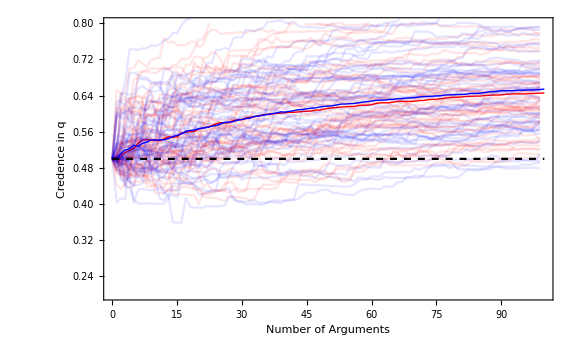

Simulation time = 129.31, pFind bounds = {1,1}, jShift bounds = {0,1}

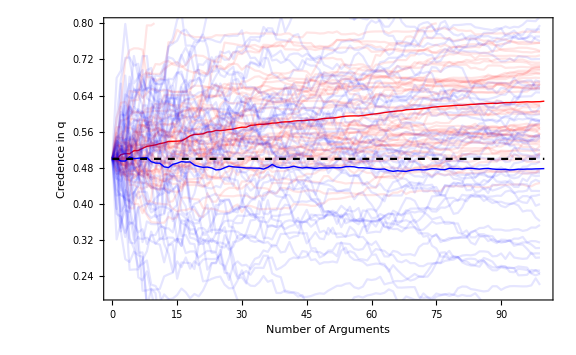

Simulation time = 138.604, pFind bounds = {0,1}, jShift bounds = {0,0.5}

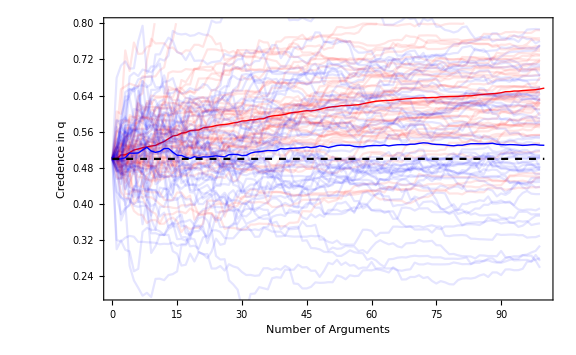

Simulation time = 146.383, pFind bounds = {0,1}, jShift bounds = {0,1}

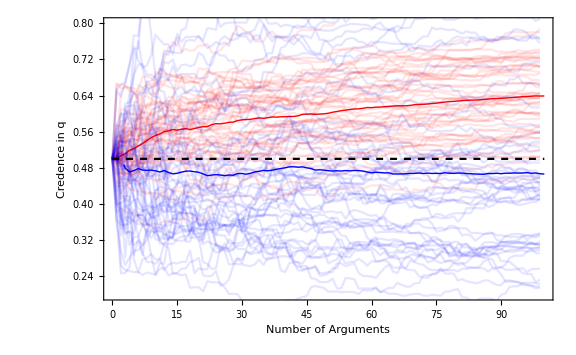

```mathematica
Clear[ag];
Clear[traj];
numAgents=50;
numArgs=100;
baseShift = 0.4;
hardenSpeed = 0.2;

Do[
pFindIter = iter[[1]];
jShiftIter = iter[[2]];
pFindBnds = {pFindIter[[1]],pFindIter[[2]]};
jShiftBnds = {jShiftIter[[1]],jShiftIter[[2]]};

simTime = Timing[Do[
(*pro agents NEVER scrutinize*)
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get an argument model:*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*update beliefs:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

(*con agents ALWAYS scrutinize:*)
If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get a favorable argument model*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*make the scrutinized model:*)
pFind = RandomReal[{pFindBnds[[1]],pFindBnds[[2]]}];
jShift =RandomReal[{jShiftBnds[[1]],jShiftBnds[[2]]}];
scrutFrame = scrutArg[frame,pFind,jShift];

(*update beliefs via scrutinized model:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = scrutFrame[[2]],
If[RandomVariate[BernoulliDistribution[pFind]]==1,
postFxn = scrutFrame[[6]],
postFxn=scrutFrame[[4]]]];
ag[cred,iter1,valence]=probability[postFxn,{2,4,6}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"pro","con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["pro"] = ag[traj,#,"pro"]&/@Range[numAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["pro"]=Table[{iter1,Mean[ag[traj,#,"pro"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];
avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["Simulation time = ``, pFind bounds = ``, jShift bounds = ``",simTime, pFindBnds, jShiftBnds]];
Print[Show[ListLinePlot[allAgents["pro"],
PlotStyle->Directive[Red,Opacity[0.1]],
PlotRange->{{0,numArgs},{0.2,0.8}},
Frame->{{True,False},{True,False}},
ImageSize->Large,
FrameLabel->{{Style["Credence in q",FontSize->14],None},{Style["Number of Arguments",FontSize->14],None}},FrameTicks->All,
FrameTicksStyle->Directive[FontSize->14]
],
ListLinePlot[avgAgents["pro"],
PlotStyle->Directive[Red,Thick]],

ListLinePlot[allAgents["con"],
PlotStyle->Directive[Blue,Opacity[0.1]]],
ListLinePlot[avgAgents["con"],
PlotStyle->Directive[Blue,Thick]],
Plot[0.5,{x,0,numArgs},PlotStyle->{Black,Dashed}]
]];
,{iter,(*first pair is pFindBnds, second is jShiftBnds*)
{
{{0,0},{0,0}},(*never find, no added ambiguity*)
{{1,1},{0,1}},(*always find, random added ambiguity*)
{{0,1},{0,0.5}}, (*random probability of find; add little ambiguity*)
{{0,1},{0,1}} (*random probability of find, add random ambiguity*)
}}]
```

### Robustness

Since what happens with our red (pro) agents is familiar from the last section, I’ll just check robustness for blue ones, who always scrutinize, using the four above settings of our parameters.

Recall that the above simulations for 100 red agents and these parameters, we had an estimate for their posterior credence at 0.663 with a 95% confidence interval of [0.642, 0.684]

(1) never find a flaw when they scrutinize (pFind = 0), no added ambiguity (jShift = 0 ):

The following simulates 100 con agents and calculates confidence intervals for mean posteriors. When I ran it, I had an estimate of 0.652 with a 95% confidence interval of [0.632, 0.674]. As expected, this is in the same range as above.

```mathematica
Clear[ag];
Clear[traj];
numAgents=200;
numArgs=100;
baseShift = 0.4;
hardenSpeed = 0.2;


pFindBnds = {0,0};
jShiftBnds = {0,0};

simTime = Timing[Do[
(*pro agents NEVER scrutinize*)
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get an argument model:*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*update beliefs:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

(*con agents ALWAYS scrutinize:*)
If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get a favorable argument model*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*make the scrutinized model:*)
pFind = RandomReal[{pFindBnds[[1]],pFindBnds[[2]]}];
jShift =RandomReal[{jShiftBnds[[1]],jShiftBnds[[2]]}];
scrutFrame = scrutArg[frame,pFind,jShift];

(*update beliefs via scrutinized model:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = scrutFrame[[2]],
If[RandomVariate[BernoulliDistribution[pFind]]==1,
postFxn = scrutFrame[[6]],
postFxn=scrutFrame[[4]]]];
ag[cred,iter1,valence]=probability[postFxn,{2,4,6}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["Simulation time = ``, pFind bounds = ``, jShift bounds = ``",simTime, pFindBnds, jShiftBnds]];
posteriors = ag[cred,#,"con"]&/@Range[numAgents];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

Simulation time = 314.121, pFind bounds = {0,0}, jShift bounds = {0,0}

0.649489

{0.635969,0.66301}

(2) Always find a flaw if there is one they scrutinize (pFind = 1); random ambiguity (jShift between 0 and 1)

The following simulates 200 con agents and calculates confidence intervals for mean posteriors. When I ran it, I had an estimate of 0.506 with a 95% confidence interval of [0.473, 0.539]. As expected, this is close to the 50% credence they begin with.

```mathematica
Clear[ag];
Clear[traj];
numAgents=200;
numArgs=100;
baseShift = 0.4;
hardenSpeed = 0.2;


pFindBnds = {1,1};
jShiftBnds = {0,1};

simTime = Timing[Do[
(*pro agents NEVER scrutinize*)
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get an argument model:*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*update beliefs:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

(*con agents ALWAYS scrutinize:*)
If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get a favorable argument model*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*make the scrutinized model:*)
pFind = 1;
jShift =RandomReal[{jShiftBnds[[1]],jShiftBnds[[2]]}];
scrutFrame = scrutArg[frame,pFind,jShift];

(*update beliefs via scrutinized model:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = scrutFrame[[2]],
If[RandomVariate[BernoulliDistribution[pFind]]==1,
postFxn = scrutFrame[[6]],
postFxn=scrutFrame[[4]]]];
ag[cred,iter1,valence]=probability[postFxn,{2,4,6}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["Simulation time = ``, pFind bounds = ``, jShift bounds = ``",simTime, pFindBnds, jShiftBnds]];
posteriors = ag[cred,#,"con"]&/@Range[numAgents];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

Simulation time = 271.641, pFind bounds = {1,1}, jShift bounds = {0,1}

0.505558

{0.472501,0.538614}

(3)Sometimes find a flaw if there is one they scrutinize (pFind between 0 and 1); small ambiguity (jShift between 0 and 0.5)

The following simulates 200 con agents and calculates confidence intervals for mean posteriors. When I ran it, I had an estimate of 0.529 with a 95% confidence interval of [0.506,0.553]. Since this is  well below the  [0.632, 0.674] confidence-interval for agents who don’t scrutinize, such scrutiny dampens the degree of predictable polarization

```mathematica
Clear[ag];
Clear[traj];
numAgents=200;
numArgs=100;
baseShift = 0.4;
hardenSpeed = 0.2;


pFindBnds = {0,1};
jShiftBnds = {0,0.5};

simTime = Timing[Do[
(*pro agents NEVER scrutinize*)
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get an argument model:*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*update beliefs:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

(*con agents ALWAYS scrutinize:*)
If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get a favorable argument model*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*make the scrutinized model:*)
pFind = RandomReal[{pFindBnds[[1]],pFindBnds[[2]]}];
jShift =RandomReal[{jShiftBnds[[1]],jShiftBnds[[2]]}];
scrutFrame = scrutArg[frame,pFind,jShift];

(*update beliefs via scrutinized model:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = scrutFrame[[2]],
If[RandomVariate[BernoulliDistribution[pFind]]==1,
postFxn = scrutFrame[[6]],
postFxn=scrutFrame[[4]]]];
ag[cred,iter1,valence]=probability[postFxn,{2,4,6}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["Simulation time = ``, pFind bounds = ``, jShift bounds = ``",simTime, pFindBnds, jShiftBnds]];
posteriors = ag[cred,#,"con"]&/@Range[numAgents];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

Simulation time = 280.341, pFind bounds = {0,1}, jShift bounds = {0,0.5}

0.529423

{0.505975,0.55287}

(4) Sometimes find a flaw if there is one they scrutinize (pFind between 0 and 1); random added ambiguity (jShift between 0 and 1)

The following simulates 200 con agents and calculates confidence intervals for mean posteriors. When I ran it, I had an estimate of 0.461 with a 95% confidence interval of [0.434,0.488]. Since this is   below the prior of 0.5, such scrutiny in fact reverses the direction of predictable polarization.

```mathematica
Clear[ag];
Clear[traj];
numAgents=200;
numArgs=100;
baseShift = 0.4;
hardenSpeed = 0.2;


pFindBnds = {0,1};
jShiftBnds = {0,1};

simTime = Timing[Do[
(*pro agents NEVER scrutinize*)
If[valence=="pro",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get an argument model:*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*update beliefs:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = frame[[2]],
postFxn = frame[[4]]
];
ag[cred,iter1,valence]=probability[postFxn,{2,4}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];

(*con agents ALWAYS scrutinize:*)
If[valence=="con",
Do[iter1;
ticker=10;
ag[cred,iter1,valence] = 0.5;
ag[traj,iter1,valence]=Reap[Do[
(*get a favorable argument model*)
priorG = RandomReal[{0,1}];
Sow[{ticker-10,ag[cred,iter1,valence]}];
frame=getRandFavShiftArgModel[ag[cred,iter1,valence],baseShift/(hardenSpeed*ticker),priorG];
(*make the scrutinized model:*)
pFind = RandomReal[{pFindBnds[[1]],pFindBnds[[2]]}];
jShift =RandomReal[{jShiftBnds[[1]],jShiftBnds[[2]]}];
scrutFrame = scrutArg[frame,pFind,jShift];

(*update beliefs via scrutinized model:*)
If[RandomVariate[BernoulliDistribution[priorG]]==1,
postFxn = scrutFrame[[2]],
If[RandomVariate[BernoulliDistribution[pFind]]==1,
postFxn = scrutFrame[[6]],
postFxn=scrutFrame[[4]]]];
ag[cred,iter1,valence]=probability[postFxn,{2,4,6}];
ticker+=1;
,numArgs]][[2,1]];
,{iter1,numAgents}]];
,{valence,{"con"}}]][[1]];
Beep[];

Clear[allAgents];
allAgents["con"] = ag[traj,#,"con"]&/@Range[numAgents];

avgAgents["con"]=Table[{iter1,Mean[ag[traj,#,"con"][[iter1,2]]&/@Range[numAgents]]},{iter1,numArgs}];

Print[StringForm["Simulation time = ``, pFind bounds = ``, jShift bounds = ``",simTime, pFindBnds, jShiftBnds]];
posteriors = ag[cred,#,"con"]&/@Range[numAgents];
Print[Mean[posteriors]];
Print[MeanCI[posteriors]];
```

Simulation time = 259.956, pFind bounds = {0,1}, jShift bounds = {0,1}

0.460863

{0.434194,0.487532}